```mathematica
ClearAll["Global`*"]
```

## Q1

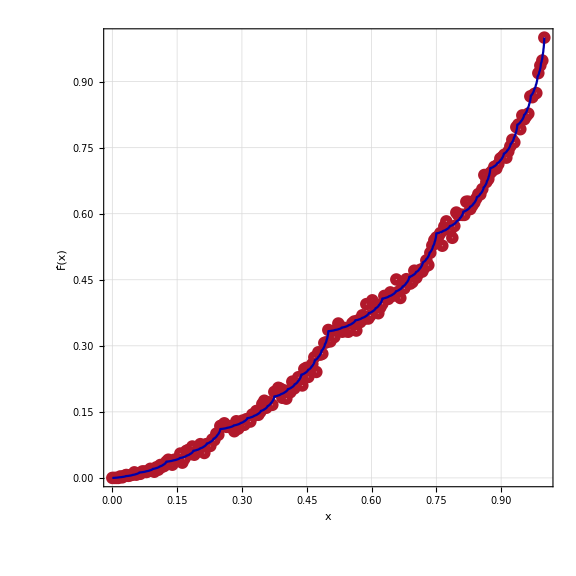

```mathematica
Q1data=Import[FileNameJoin[{NotebookDirectory[],"Q1.csv"}]];
Q1line=Import[FileNameJoin[{NotebookDirectory[],"Q1line.csv"}]];
p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];

Show[ListPlot[Q1data,FrameLabel->{"x","F̂(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick],ListLinePlot[Q1line,PlotStyle->Darker[Blue]]]
```

## Q3

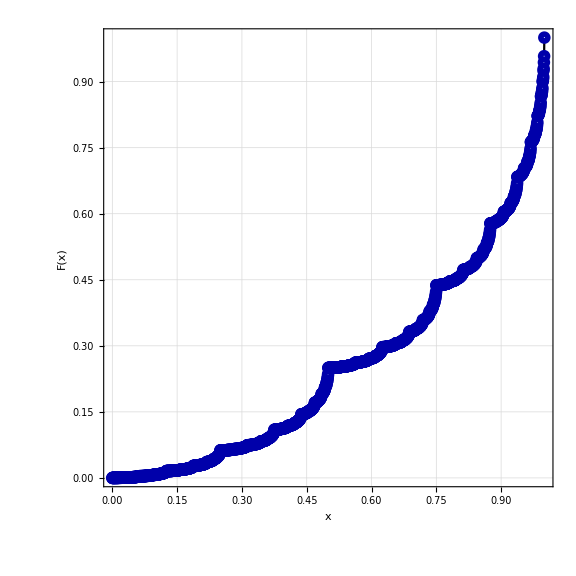

```mathematica
Q3data=Import[FileNameJoin[{NotebookDirectory[],"Q3.csv"}]];
p1=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];

ListPlot[Q3data,FrameLabel->{"x","F(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,Joined->True]
```

## Q4

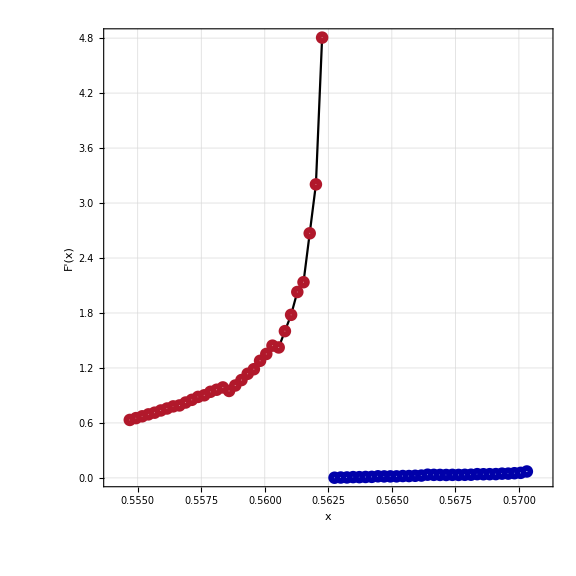

```mathematica
Q4ldata=Import[FileNameJoin[{NotebookDirectory[],"Q4l.csv"}]];
Q4rdata=Import[FileNameJoin[{NotebookDirectory[],"Q4r.csv"}]];
p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];
p=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
Show[ListPlot[Q4ldata,FrameLabel->{"x","F'(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,PlotRange->{{0.554,0.571},All},Joined->True],ListPlot[Q4rdata,FrameLabel->{"x","F'(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,PlotRange->{{0.554,0.571},All},Joined->True]]
```

## Q6

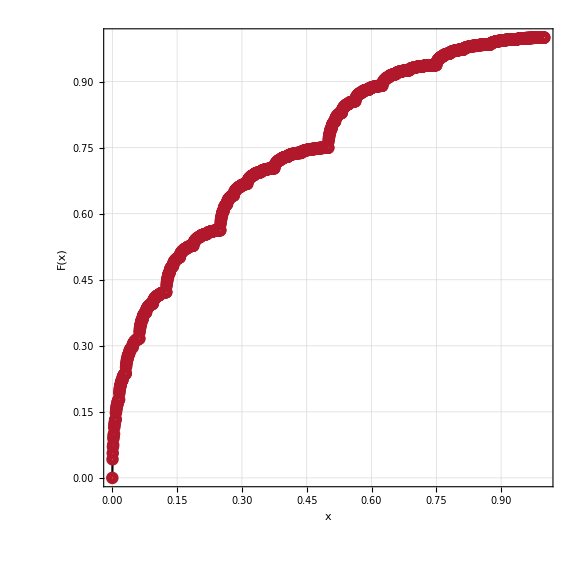

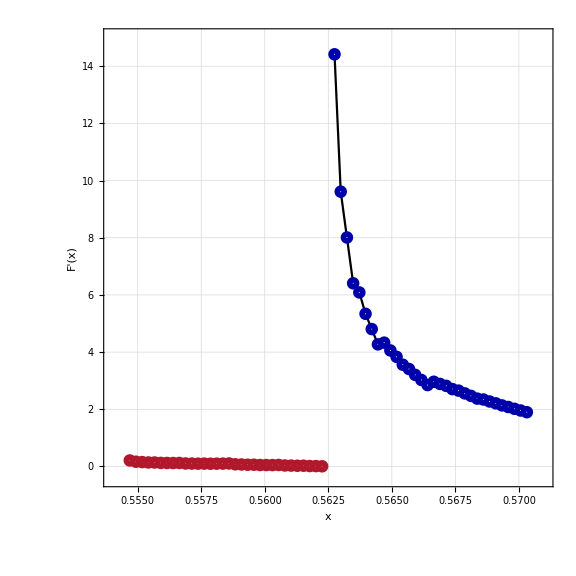

```mathematica
Q61=Import[FileNameJoin[{NotebookDirectory[],"Q6-1.csv"}]];
Q61l=Import[FileNameJoin[{NotebookDirectory[],"Q6-1l.csv"}]];
Q61r=Import[FileNameJoin[{NotebookDirectory[],"Q6-1r.csv"}]];
p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];
p=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
ListPlot[Q61,FrameLabel->{"x","F(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,Joined->True]
Show[ListPlot[Q61l,FrameLabel->{"x","F'(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,PlotRange->{{0.554,0.571},{-0.4,15}},Joined->True],ListPlot[Q61r,FrameLabel->{"x","F'(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,PlotRange->{{0.554,0.571},All},Joined->True]]
```

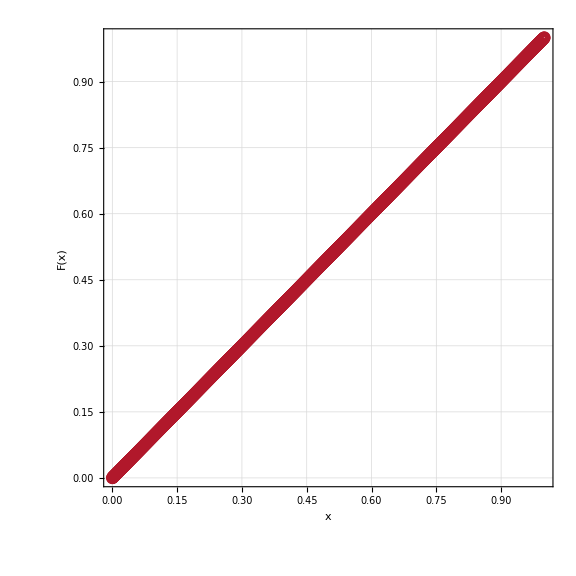

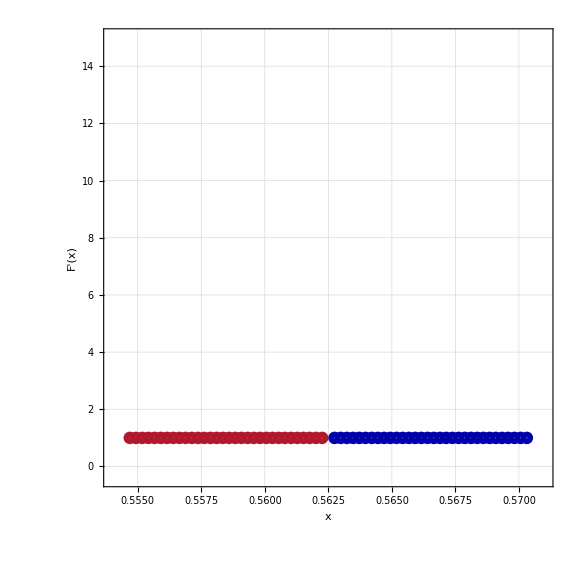

```mathematica
Q62=Import[FileNameJoin[{NotebookDirectory[],"Q6-2.csv"}]];
Q62l=Import[FileNameJoin[{NotebookDirectory[],"Q6-2l.csv"}]];
Q62r=Import[FileNameJoin[{NotebookDirectory[],"Q6-2r.csv"}]];
p1=Graphics[{EdgeForm[{RGBColor[0.694118, 0.0941176, 0.168627],Thickness[0.3]}],FaceForm[RGBColor[0.847059, 0.545098, 0.584314]],Disk[]}];
p=Graphics[{EdgeForm[{Darker[Blue],Thickness[0.3]}],FaceForm[LightBlue],Disk[]}];
ListPlot[Q62,FrameLabel->{"x","F(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,Joined->True]
Show[ListPlot[Q62l,FrameLabel->{"x","F'(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p1,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,PlotRange->{{0.554,0.571},{-0.4,15}},Joined->True],ListPlot[Q62r,FrameLabel->{"x","F'(x)"},LabelStyle->{FontSize->20, Black},ImageSize->Large, Frame->True,GridLines->Automatic,PlotMarkers->{p,.015},GridLinesStyle->Directive[RGBColor[0.733333, 0.968627, 0.952941],Dashed], PlotStyle->GrayLevel[0],PlotMarkers->{Automatic}, FrameTicksStyle->Directive[Black,16], AspectRatio->1,FrameStyle->Thick,PlotRange->{{0.554,0.571},All},Joined->True]]
```